```mathematica
ClearAll["Global`*"]
w=2/3;
period=2*Pi/w;
A=1.5;
tmax=1000;
init=0.2
primeInit=0
naac=1000; (*points per natural period of pendulum w=1*)
soln=ParametricNDSolve[{theta''[t]+(1/Q) * theta'[t]+Sin[theta[t]]==A  Cos[w t],theta[0]==init,theta'[0]==primeInit},theta,{t,0,tmax},{Q}];
```

0.2

0

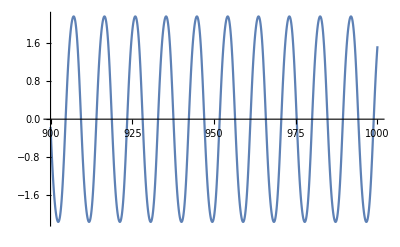

```mathematica
Q=1;
Plot[theta[Q][x]/.soln,{x,tmax-100,tmax}]
```

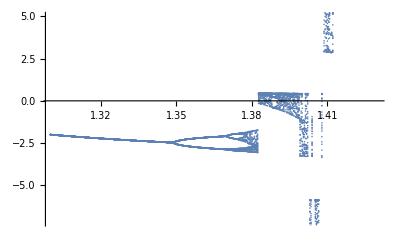

```mathematica
tdel=period;
Qmin=1.3;
Qmax=1.43;
numQPoints=300;
Qres=numQPoints/(Qmax-Qmin);
offset=0;
start=tdel*70+offset;
end=tdel*100+offset;
length=Length[Table[x,{x,start,end,tdel}]];
bifur=Flatten[Table[Transpose[{
ConstantArray[i,length],Flatten[Table[theta[i][x]/.soln,{x,start,end,tdel}]]}],
{i,Qmin,Qmax,1/Qres}],1];
ListPlot[bifur]
```